## Defining functions

Functions are just another type of expression in Mathematica

Their argument lists take the form of patterns. We will discuss patterns in more depth in the next lecture

For now, we will make use of one kind of pattern: x_
which matches any expression and calls it x.
For example:

```mathematica
addOne[x_]:=x+1
```

This function can be called with any kind of argument. That argument will be called x in the body of the function, which gives a result by adding one

```mathematica
addOne[2]
```

3

```mathematica
addOne[{3,4,5}]
```

{4,5,6}

There are much more sophisticated patterns than just “match any expression.” We will cover these later.

Suppose we want to recursively compute the factorial
Base case: fac(0) = 1
Recursive definition: fac(n) = n*fac(n-1)

This is simple to define in Mathematica.
We begin with the base case

```mathematica
fac[0]:=1
```

Now, fac[0] will evaluate to 1

```mathematica
fac[0]
```

1

We don’t have a rule for the general case, so fac[n] will remain unevaluated:

```mathematica
fac[1]
```

fac[1]

Defining the general case:

```mathematica
fac[n_]:=n*fac[n-1]
```

```mathematica
fac[1]
```

1

```mathematica
fac[10]
```

3628800

```mathematica
10!
```

3628800

Let’s do a similar exercise with the Fibonacci sequence:
F_0=0
F_1=1
F_n=F_(n-1)+F_(n-2)

```mathematica
fib[0]:=0
fib[1]:=1
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib[10]
```

55

Of course, Mathematica also has this built in, so we can check our work...

```mathematica
Fibonacci[10]
```

55

## Solving recurrence relations

Suppose we have the recurrence relation

a_0=2
a_1=3
a_n=7 a_(n-1)-10 a_(n-2)

We can easily create a function to recursively evaluate this sequence

```mathematica
a[0]:=2
a[1]:=3
a[n_]:=7a[n-1]-10a[n-2]
```

```mathematica
a[10]
```

-3252819

What if we want to know a general (non-recursive formula)?
First, concentrate on the recursive definition a_n=7 a_(n-1)-10 a_(n-2) (ignoring boundary conditions)
We can solve this recurrence by making the ansatz that a_nis given by r^n for some r
In that case,

r^(n-2)(r^2-7r+10)=0

So, we look for solutions to this equation.

```mathematica
Factor[r^2-7r+10]
```

(-5+r) (-2+r)

So, r=5 and r=2 satisfy this relationship.
The general solution will be given by a_n=c*5^n+d*2^n

We can easily solve the system of equations to find the values of c and d.
But we can also let Mathematica help...

```mathematica
expr=c*5^n+d*2^n
case0=expr/.n->0
case1=expr/.n->1
```

5^n c+2^n d

c+d

5 c+2 d

```mathematica
soln=Solve[{case0==2,case1==3},{c,d}]
```

{{c→-1/3,d→7/3}}

Let’s check our formula

```mathematica
expr/.soln⟦1⟧
```

(7 2^n)/3-5^n/3

```mathematica
(expr/.soln⟦1⟧/.n->10 )==a[10]
```

True

ClearAll deletes all the definitions we made for a

```mathematica
ClearAll[a]
```

Mathematica can also solve the recurrence directly using RSolve

```mathematica
RSolve[{a[0]==2,a[1]==3,a[n]==7a[n-1]-10a[n-2]},a,n]
```

{{a→Function[{n},1/3 (7 2^n-5^n)]}}

## More complicated functions and local variables

Sometimes we want to introduce local variables in a function for intermediate values in long calculations

This can be achieved using Module

```mathematica
{x,y,z}
```

{0.714824,0.255667,z}

```mathematica
Module[{x,y,z},
(* 
 (This is a comment by the way)
x, y, and z are declared as local variables
*)
x=1;
y=x+1;
z=y*2;
Print[{x,y,z}];
]
```

{1,2,4}

```mathematica
Print[{x,y,z}]
```

{0.714824,0.0801186,z}

Mathematica also has other scoping mechanisms (i.e. for creating variables with local scope)
See e.g. Block, With

For our uses, Module is sufficient

## Functional style programming

Mathematica is a multi-paradigm programming language

It supports both functional and imperative programming, but functional constructs are often very natural

For example, applying a function f to a list is known as mapping f over the list

```mathematica
mylist=Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Map[Sqrt,mylist]
```

{1,2,3,4,5,6,7,8,9,10}

Map is considered so important in Mathematica it has its own syntax

```mathematica
Sqrt/@mylist
```

{1,2,3,4,5,6,7,8,9,10}

We can define more complicated functions if we want

```mathematica
f[x_]:=Sin[Sqrt[x]+x^(2/3)]
```

```mathematica
Map[f,mylist]
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

Sometimes we want to create an anonymous function so that we don’t need to name it

```mathematica
Map[Sin[Sqrt[#]+#^(2/3)]&,mylist]
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

Here # indicates the argument, and & tells Mathematica that the preceding expression is a function

This notation can easily become hard to read, so be careful

```mathematica
Sin[Sqrt[#]+#^(2/3)]&/@mylist
```

{Sin[2],Sin[2+2 2^(1/3)],Sin[3+3 3^(1/3)],Sin[4+4 2^(2/3)],Sin[5+5 5^(1/3)],Sin[6+6 6^(1/3)],Sin[7+7 7^(1/3)],Sin[24],Sin[9+9 3^(2/3)],Sin[10+10 10^(1/3)]}

## More functional programming

Recall our list

```mathematica
mylist
```

{1,4,9,16,25,36,49,64,81,100}

We can apply filters to the list using Select

```mathematica
Select[mylist,EvenQ]
```

{4,16,36,64,100}

We can combine this with anonymous functions

```mathematica
Select[mylist,#>20&]
```

{25,36,49,64,81,100}

Sometimes we want to apply a function to a list for its side-effect rather than its return-value

For this we have Scan

```mathematica
Scan[Print[Sqrt[#]]&,mylist]
```

1

2

3

4

5

6

7

8

9

10

There are a ton more functional programming facilities in Mathematica

See e.g. Nest, Fold, Apply

```mathematica
mylist=RandomInteger[{1,50},20]
```

{49,26,21,18,45,11,32,29,38,46,9,46,44,32,5,50,45,43,30,1}

Can we get the sum of all of these entries?

```mathematica
Plus[mylist]
```

{49,26,21,18,45,11,32,29,38,46,9,46,44,32,5,50,45,43,30,1}

```mathematica
Plus[{1,2,3}]
```

{1,2,3}

```mathematica
Plus[1,2,3]
```

6

```mathematica
Apply[Plus,mylist]
```

620

```mathematica
Total[mylist]
```

620

## Patterns

We have seen one type of pattern before: x_

The underscore will match any expression, and then the result will be called x

We can test if a pattern matches an expression using MatchQ

```mathematica
MatchQ[1,x_]
```

True

```mathematica
MatchQ["Anything will match the pattern x_",x_]
```

True

There are other kinds of patterns.

Except will match anything except what’s in the brackets

```mathematica
MatchQ[2,Except[1]]
```

True

```mathematica
MatchQ[1,Except[1]]
```

False

You can match for specific heads of expressions with _h

```mathematica
MatchQ[1,n_Integer]
```

True

```mathematica
MatchQ[2/3,n_Integer]
```

False

Conditions can be added to a pattern with /;

```mathematica
MatchQ[-1.5,n_/;n<0]
```

True

```mathematica
MatchQ[4,n_/;n<0]
```

False

Boolean functions can also be added with the ? operator

```mathematica
MatchQ[4,n_?EvenQ]
```

True

```mathematica
MatchQ[5,n_?EvenQ]
```

False

Patterns can be combined using | for or

```mathematica
MatchQ[5,_?EvenQ|5]
```

True

## Type checking

Checking for specific heads allows us to perform type checking

```mathematica
fib[0]:=0
fib[1]:=1
fib[n_Integer]:=fib[n-1]+fib[n-2]
fib[_]:=Print["fib must be called with integer argument"]
```

```mathematica
DownValues[fib]
```

{HoldPattern[fib[0]]:>0,HoldPattern[fib[1]]:>1,HoldPattern[fib[n_Integer]]:>fib[n-1]+fib[n-2],HoldPattern[fib[_]]:>Print[fib must be called with integer argument]}

```mathematica
fib[5]
```

5

```mathematica
fib[2/3]
```

fib must be called with integer argument

```mathematica
fib[-1]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fib[-1023-1].

Hold[fib[-1-1]+fib[-1-2]]

Let’s get rid of our old (overly-general) rule

```mathematica
fib[n_Integer]=.
```

We want to add a condition to the pattern: only match non-negative integers

```mathematica
fib[n_Integer/;n≥0]:=fib[n-1]+fib[n-2]
fib[_]:=Print["fib must be called with non-negative integer argument"]
```

```mathematica
fib[-1]
```

fib must be called with non-negative integer argument

Another example

```mathematica
abs[x_/;x≥0]:=x
abs[x_/;x<0]:=-x
```

```mathematica
abs[10]
```

10

```mathematica
abs[-10]
```

10

## Example: defining our own derivative function

We want to differentiate arbitrary expressions

This can be achieved using the basic rules of differentiation:

Linearity

Product rule

Chain rule

We first need the concept of an expression being independent of another expression.
This is achieved using FreeQ

```mathematica
FreeQ[y^2,x]
```

True

```mathematica
FreeQ[y*x,x]
```

True

Some common base cases:

```mathematica
diff[x_,x_]:=1
diff[c_,x_]/;FreeQ[c,x]:=0
```

Addition:

```mathematica
diff[f_+g_,x_]:=diff[f,x]+diff[g,x]
```

Scalar multiplication:

```mathematica
diff[c_*f_,x_]/;FreeQ[c,x]:=c*diff[f,x]
```

Product rule

```mathematica
diff[f_*g_,x_]:=diff[f,x]*g+diff[g,x]*f
```

Chain rule

```mathematica
diff[f_[g_],x_]/;!MatchQ[g,x]:=diff[f[g],g]diff[g,x]
```

(Have to be careful in the above not to match f[x] (so make sure g doesn’t match x), otherwise have infinite recursion)

```mathematica
diff[f_^n_,x_]/;FreeQ[n,x]:=n*f^(n-1)*diff[f,x]
```

```mathematica
poly=Expand[(x+1)^10]
```

348.438

```mathematica
diff[poly,x]
```

0

```mathematica
D[poly,x]
```

General::ivar: 0.795612 is not a valid variable.

∂_0.795612 348.438

If we encounter functions whose derivatives we don’t know, it will leave them unevaluated:

```mathematica
diff[Sin[x]Cos[x],x]
```

0

```mathematica
diff[Sin[x^2],x]
```

0

We can easily add rules for trigonometric functions:

```mathematica
diff[Sin[x_],x_]:=Cos[x]
diff[Cos[x_],x_]:=-Sin[x]
```

```mathematica
diff[Sin[x^2],x]
```

0

```mathematica
diff[Sin[x]Cos[x],x]
```

0

Our definitions will automatically work with function composition:

```mathematica
diff[Sin[x^2]Cos[x^3],x]
```

0

```mathematica
Trace[diff[Sin[x^2]Cos[x^3],x]]
```

{{{{{x,0.795612},0.795612^2,0.632999},Sin[0.632999],0.591565},{{{x,0.795612},0.795612^3,0.503622},Cos[0.503622],0.875841},0.591565 0.875841,0.518117},{x,0.795612},diff[0.518117,0.795612],{FreeQ[0.518117,0.795612],True},0}

```mathematica
D[Sin[x^2]Cos[x^3],x]
```

General::ivar: 0.795612 is not a valid variable.

∂_0.795612 0.518117

## Speed: memoization

Recall our Fibonacci sequence

```mathematica
fib[0]:=0
fib[1]:=1
fib[n_]:=fib[n-1]+fib[n-2]
```

How fast (slow?) is it?

```mathematica
Timing[fib[20]]
```

{0.016944,6765}

```mathematica
Timing[fib[25]]
```

{0.185652,75025}

```mathematica
Timing[fib[30]]
```

{2.0178,832040}

```mathematica
timings=Table[Timing[fib[i]]⟦1⟧,{i,1,30}]
```

{7.×10^-6,0.000011,8.×10^-6,0.000011,0.000016,0.000027,0.000042,0.000071,0.000112,0.000178,0.000292,0.000422,0.000681,0.001112,0.001709,0.002643,0.003857,0.006279,0.010399,0.016571,0.026514,0.043862,0.069313,0.113726,0.182523,0.291275,0.46843,0.767646,1.23221,1.98911}

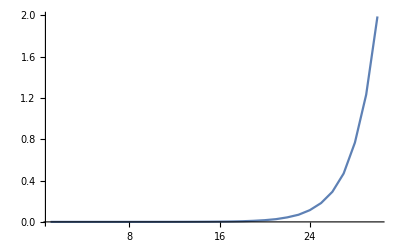

```mathematica
timingplt=ListPlot[timings,Joined->True,PlotRange->All]
```

In fact, the runtime for the recursive algorithm satisfies

T_n=T_(n-1)+T_(n-2)

and so the time to compute fib[n] is actually given by fib[n]

We can easily find a closed form representation of the Fibonacci sequence (involving the golden ratio) using e.g. the characteristic polynomial

```mathematica
FullSimplify[FunctionExpand[Fibonacci[n]],{n∈Integers}]
```

-((-2/(1+√5))^n-(1/2 (1+√5))^n)/(√5)

```mathematica
factor=(timings⟦30⟧/GoldenRatio^30);
```

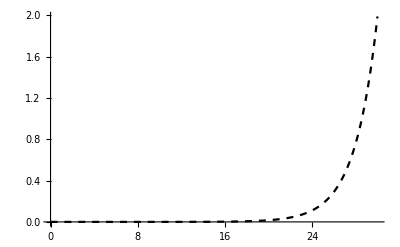

```mathematica
estimateplt=Plot[GoldenRatio^n*factor,{n,0,30},PlotRange->All,PlotStyle->{Black,Dashed}]
```

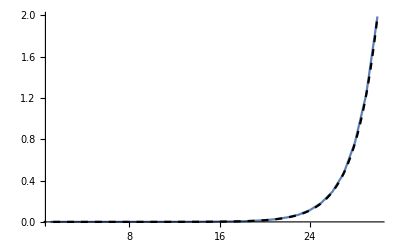

```mathematica
Show[{timingplt,estimateplt}]
```

We can try to optimize our recursive implementation using memoization

```mathematica
Trace[fib[10]]
```

{fib[10],{10≥0,True},fib[10-1]+fib[10-2],{{10-1,9},fib[9],{9≥0,True},fib[9-1]+fib[9-2],{{9-1,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},{{9-2,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},21+13,34},{{10-2,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},34+21,55}

Look how many times fib[1] and fib[0] are evaluated! We can speed things up by storing these values

```mathematica
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

```mathematica
Trace[fib[10]]
```

{fib[10],{10≥0,True},fib[10-1]+fib[10-2],{{10-1,9},fib[9],{9≥0,True},fib[9-1]+fib[9-2],{{9-1,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},{{9-2,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},21+13,34},{{10-2,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},34+21,55}

```mathematica
Trace[fib[15]]
```

1
 |  |  |  |

```mathematica
Trace[fib[10]]
```

{fib[10],{10≥0,True},fib[10-1]+fib[10-2],{{10-1,9},fib[9],{9≥0,True},fib[9-1]+fib[9-2],{{9-1,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},{{9-2,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},21+13,34},{{10-2,8},fib[8],{8≥0,True},fib[8-1]+fib[8-2],{{8-1,7},fib[7],{7≥0,True},fib[7-1]+fib[7-2],{{7-1,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},{{7-2,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},8+5,13},{{8-2,6},fib[6],{6≥0,True},fib[6-1]+fib[6-2],{{6-1,5},fib[5],{5≥0,True},fib[5-1]+fib[5-2],{{5-1,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},{{5-2,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},3+2,5},{{6-2,4},fib[4],{4≥0,True},fib[4-1]+fib[4-2],{{4-1,3},fib[3],{3≥0,True},fib[3-1]+fib[3-2],{{3-1,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},{{3-2,1},fib[1],1},1+1,2},{{4-2,2},fib[2],{2≥0,True},fib[2-1]+fib[2-2],{{2-1,1},fib[1],1},{{2-2,0},fib[0],0},1+0,1},2+1,3},5+3,8},13+8,21},34+21,55}

```mathematica
bench[n_]:=Module[{myfib},
myfib[0]:=0;
myfib[1]:=1;
myfib[m_]:=myfib[m]=myfib[m-1]+myfib[m-2];
myfib[n]]
```

```mathematica
newtimings=Table[Timing[bench[i]]⟦1⟧,{i,1,30}]
```

{0.000046,0.000028,0.00003,0.000031,0.000036,0.000039,0.000044,0.000047,0.000052,0.000057,0.000063,0.000068,0.000075,0.000078,0.000084,0.000088,0.000101,0.000104,0.000105,0.000109,0.000111,0.000116,0.000118,0.000123,0.000128,0.000129,0.000133,0.000136,0.00014,0.000142}

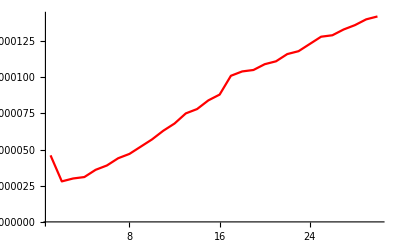

```mathematica
newtimingplt=ListPlot[newtimings,Joined->True,PlotRange->All,PlotStyle->Red]
```

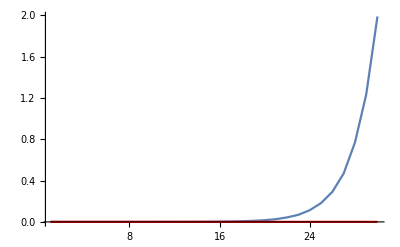

```mathematica
Show[timingplt,newtimingplt]
```

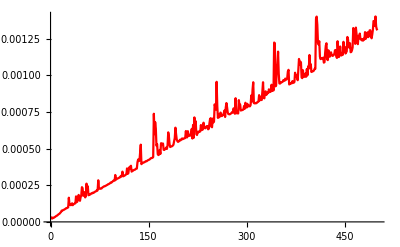

```mathematica
Table[Timing[bench[i]]⟦1⟧,{i,1,500}];
ListPlot[%,Joined->True,PlotRange->All,PlotStyle->Red]
```

We can see that the timings are linear, which is clear given the recurrence

T_n=T_(n-1)+1